## Problem 5.5

```mathematica
A=(Sin[theta])^2*no^2+(Cos[theta])^2*ne^2;
B=no^2*ne^2+no^4*Sin[theta]^2+ne^2*no^2*Cos[theta]^2;
c=no^4*ne^2;
```

```mathematica
Simplify[B^2-4*A*c]
```

no^4 (ne^2-no^2)^2 Sin[theta]^4

```mathematica
Simplify[(B + Sqrt[B^2-4*A*c])/(2*A)]
```

(ne^2 no^2+ne^2 no^2 Cos[theta]^2+no^4 Sin[theta]^2+√(no^4 (ne^2-no^2)^2 Sin[theta]^4))/(2 (ne^2 Cos[theta]^2+no^2 Sin[theta]^2))

```mathematica
Simplify[(B - Sqrt[B^2-4*A*c])/(2*A)]
```

(ne^2 no^2+ne^2 no^2 Cos[theta]^2+no^4 Sin[theta]^2-√(no^4 (ne^2-no^2)^2 Sin[theta]^4))/(2 (ne^2 Cos[theta]^2+no^2 Sin[theta]^2))

## Problem 5.7

```mathematica
no = 1.54424;
ne=1.55335;
lambda=633*10^-9;
d=0.96*10^-3;
dc=Pi/180;
np=(no*ne)/Sqrt[no^2*(Sin[thetap])^2+ne^2*(Cos[thetap])^2];
delta=d*(Tan[thetas]-Tan[thetap])*Sin[thetai*dc];
thetas=ArcSin[Sin[thetai*dc]/no];
thetap=ArcSin[Sin[thetai*dc]/ne];
```

```mathematica
s=d/((lambda/no)*Cos[thetas]);
p=d/((lambda/np)*Cos[thetap])+delta/lambda;
```

```mathematica
deltaphi=2*Pi*(p-s)//Simplify
```

-14715.1/(√(1-0.419344 Sin[(π thetai)/180]^2))+22857.6/(√(1-0.41444 Sin[(π thetai)/180]^2) √(2.4129-0.0116951 Sin[(π thetai)/180]^2))+Sin[(π thetai)/180]^2 (6170.67/(√(1-0.419344 Sin[(π thetai)/180]^2))-6134.48/(√(1-0.41444 Sin[(π thetai)/180]^2)))

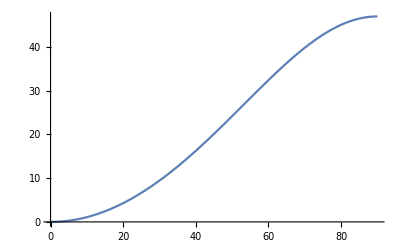

```mathematica
Plot[deltaphi,{thetai,0,90}]
```